```mathematica
(*importar dados do excel*)
```

```mathematica
s=Import["C:\\Users\\Utilizador\\Documents\\astropi\\2orb-data.csv"];
```

```mathematica
(*ler dados: campo magnetico (cx,cy,cz) e dados orbitais*)
```

```mathematica
Do[cx[i]=s[[i,1]],{i,1,4871}]
```

```mathematica
Do[cy[i]=s[[i,2]],{i,1,4871}]
```

```mathematica
Do[cz[i]=s[[i,3]],{i,1,4871}]
```

```mathematica
Do[lat[i]=s[[i,4]]*Pi/180,{i,1,4871}]
```

```mathematica
Do[lon[i]=s[[i,5]]*Pi/180,{i,1,4871}]
```

```mathematica
Do[alt[i]=s[[i,6]]/1000000,{i,1,4871}]
```

```mathematica
Do[tt[i]=s[[i,7]],{i,1,4871}]
```

```mathematica
tt[1]=0;
```

```mathematica
Do[tt[i]=tt[i]+tt[i-1],{i,2,4871}]
```

```mathematica
(*cálculo da distancia ao centro da terra a partir da altitude*)
```

```mathematica
a=6.378137;
```

```mathematica
b=6.356752314245;
```

```mathematica
Do[ss[i]=a^2/Sqrt[a^2*Cos[lat[i]]^2+b^2*Sin[lat[i]]^2],{i,1,4871}]
```

```mathematica
(*cálculo de z (norte), x e y (x aponta na direcao do meridiano de greenwich)*)
```

```mathematica
Do[x[i]=(alt[i]+ss[i])*Cos[lat[i]]*Cos[lon[i]],{i,1,4871}]
```

```mathematica
Do[y[i]=(alt[i]+ss[i])*Cos[lat[i]]*Sin[lon[i]],{i,1,4871}]
```

```mathematica
Do[z[i]=(alt[i]+ss[i])*Sin[lat[i]],{i,1,4871}]
```

```mathematica
(*modulo do campo magnetico*)
```

```mathematica
Do[mc[i]=Sqrt[cx[i]^2+cy[i]^2+cz[i]^2],{i,1,4871}]
```

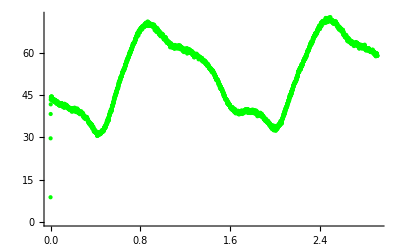

```mathematica
g1=ListPlot[Table[{tt[i]/3600,mc[i]},{i,1,4871}],PlotRange->{{0,2.91},{0,73}},PlotStyle->Green]
```

```mathematica
(*leitura de momentos multipolares do excel*)
```

```mathematica
mg=Import["C:\\Users\\Utilizador\\Documents\\astropi\\wmg2021.csv"];
```

```mathematica
mh=Import["C:\\Users\\Utilizador\\Documents\\astropi\\wmh2021.csv"];
```

```mathematica
(*construcao das matrizes dos momentos multipolares*)
```

```mathematica
h=Table[0,{i,13},{j,1,14}];
```

```mathematica
g=Table[0,{i,13},{j,1,14}];
```

```mathematica
Do[g[[i,j]]=mg[[i*(i+1)/2-1+j]][[1]],{i,1,13},{j,1,i+1}]
```

```mathematica
Do[h[[i,j]]=mh[[i*(i+1)/2-1+j]][[1]],{i,1,13},{j,1,i+1}]
```

```mathematica
(*raio da terra no modelo multipolar e ordem da expansao*)
```

```mathematica
rt=6.3712;
```

```mathematica
n=13;
```

```mathematica
(*campo no modelo multipolar*)
```

```mathematica
V[r_,la_,lo_]:=rt*Sum[(rt/r)^(i+1)*(g[[i,j]]*Cos[(j-1)*lo]+h[[i,j]]*Sin[(j-1)*lo])*LegendreP[i,j-1,Sin[la]]*(-1)^(j-1)*Sqrt[(2-KroneckerDelta[j,1])*(i-j+1)!/(i+j-1)!],{i,1,n},{j,1,i+1}]/1000
```

```mathematica
dvr[r_,la_,lo_]:=D[V[x,la,lo],x]/.x->r
```

```mathematica
dvla[r_,la_,lo_]:=D[V[r,x,lo],x]/r/.x->la
```

```mathematica
dvlo[r_,la_,lo_]:=D[V[r,la,x],x]/r/Cos[la]/.x->lo
```

```mathematica
Bx[r_,la_,lo_]:=(-Cos[la]*dvr[r,la,lo]+Sin[la]*dvla[r,la,lo])*Cos[lo]+Sin[lo]*dvlo[r,la,lo]
```

```mathematica
By[r_,la_,lo_]:=(-Cos[la]*dvr[r,la,lo]+Sin[la]*dvla[r,la,lo])*Sin[lo]-Cos[lo]*dvlo[r,la,lo]
```

```mathematica
Bz[r_,la_,lo_]:=-Sin[la]*dvr[r,la,lo]-Cos[la]*dvla[r,la,lo]
```

```mathematica
(*modulo do campo no modelo multipolar*)
```

```mathematica
B[r_,la_,lo_]:=Sqrt[Bx[r,la,lo]^2+By[r,la,lo]^2+Bz[r,la,lo]^2]
```

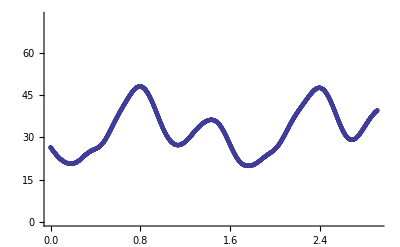

```mathematica
g2=ListPlot[Table[{tt[i]/3600,B[ss[i]+alt[i],lat[i],lon[i]]},{i,1,4871}],PlotRange->{{0,2.91},{0,73}}]
```

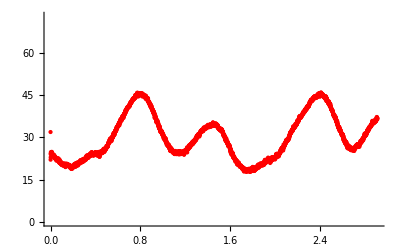

```mathematica
g3=ListPlot[Table[{tt[i]/3600,Sqrt[(cx[i]+9.666776674337207)^2+(cy[i]-15.155767368319536)^2+(cz[i]-34.335130083874944)^2]},{i,1,4871}],PlotRange->{{0,2.91},{0,73}},PlotStyle->Red]
```

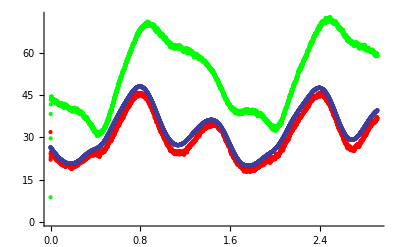

```mathematica
Show[g3,g2,g1]
```